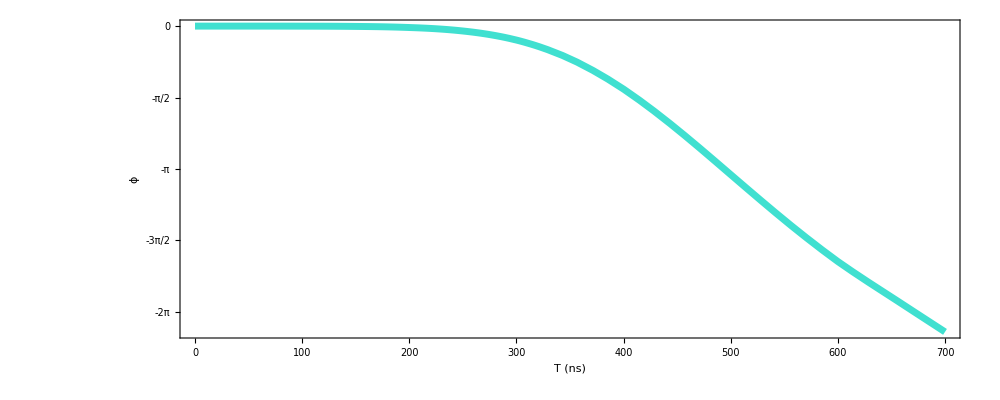

CZgateAngles.eps

```mathematica
(* gate time, CPHASE angle ϕ, local z angle, probability of nonadiabaticity *)
CphaseParams = {{0,0.,0.,0.},{1/20000000,-9.232973155291553*^-6,-1.532548118149868,0.000057773185792697745},{1/10000000,-0.0012054558671180297,2.9228455365755335,0.00007759313125788037},{3/20000000,-0.006970960658547744,1.0778310023227762,0.00009305145262872294},{1/5000000,-0.03089480230719513,-0.8282499833159402,0.00007445781705539556},{1/4000000,-0.10728948265079716,-2.8878212628534423,-0.000011464536131766678},{3/10000000,-0.3066108111696012,1.0224422366612704,0.00016027575275834316},{7/20000000,-0.7174138674561201,-1.8674065294652742,0.00013110657099546508},{1/2500000,-1.3853466861696646,0.8386389835898617,0.0000621860747545},{9/20000000,-2.2690993545931453,2.7862204928243157,0.0005013376531957103},{1/2000000,3.017694861889161,-2.2852390449953903,0.00011230107572568482},{11/20000000,2.0198033376356967,-1.7356089345599475,0.0004621473701515999},{3/5000000,1.1059698489739225,-1.755688360733958,0.000038080516564731326},{13/20000000,0.32617884428701494,-0.8969364856026468,0.00003133108181208044},{7/10000000,-0.44094851815804487,0.25457277566402653,0.000047812167818239715},{3/4000000,-1.207989450078396,1.4061924995398791,-0.000015377887106371446},{1/1250000,-1.975153562797277,2.5576729240030964,5.806039141020847*^-6},{17/20000000,-2.742167955112885,-2.5738761987477665,-0.000044058076343667096},{9/10000000,2.773818615195324,-1.4224195602978231,-0.000026457296835813437},{19/20000000,2.00682780236937,-0.27076991820889384,-0.000054904572871716795},{1/1000000,1.239606470244728,0.8806728979113698,-0.000046559464953688234}};

unravel[input_] := (
output = input;
Do[(
If[output[[i + 1]] - output[[i]] > π, output[[i + 1;;]] = output[[i + 1;;]] - 2π];
If[output[[i + 1]] - output[[i]] < -π, output[[i + 1;;]] = output[[i + 1;;]] + 2π];
),{i, Length[input] - 1}
];
output
)
Do[
CphaseParams[[All, i]] = unravel[CphaseParams[[All, i]]],
{i, {2, 4}}];

ϕFn = Interpolation[CphaseParams[[All, {1, 2}]]];


(*Figure[{
FigurePanel[{
FigGraphics[
Plot[ϕFn[T*10^-9], {T, 0, 1000}, PlotStyle->Blue]
]
},
XPlotRange->{0, 700}, XFrameLabel->"T (ns)",
YPlotRange->{-2π - .5, 0 + .3}, YFrameLabel->"ϕ", YTicks->LinTicksPi[-3π, π, π/2, 4, {"-3π", "-5π/2", "-2π", "-3π/2", "-π", "-π/2", "0", "π/2", "π"}]
];
},CanvasSize->{5,2}]*)


labelFontSize = 38;
legendFontSize = 32;
xLabel = "T (ns)";
yLabel = "ϕ";
curveThickness = 5;
curveOpacity = .5;

xTicks = LinTicks[0, 1000,100, 5, TickLengthScale->2,TickLabelStep->1];
xxTicks = LinTicks[0, 1000,100, 5, TickLengthScale->2,TickLabelStep->1, ShowTickLabels->False];
yTicks = LinTicksPi[-3π, π, π/2, 4, {"-3π", "-5π/2", "-2π", "-3π/2", "-π", "-π/2", "0", "π/2", "π"}];
yyTicks = LinTicksPi[-3π, π, π/2, 4, Table["", {i, 9}]];

Show[
Plot[ϕFn[T*10^-9], {T, 0, 700},
PlotRange->{{0, 700}, All},LabelStyle->{FontFamily-> "Times"},
PlotStyle->{
{AbsoluteThickness[curveThickness],Turquoise}
},
Axes->False
],
LabelStyle->{FontFamily-> "Times"},ImageSize->{1000, 1000},AspectRatio->.4,
FrameStyle->Directive[Thick,labelFontSize,Black],Frame->True,
FrameLabel->{Style[xLabel,labelFontSize],Style[yLabel,labelFontSize]},
FrameTicks->{xTicks,yTicks,xxTicks,yyTicks}
]

Export["CZgateAngles.eps", %]
```